```mathematica
filelist=("E:\\_time_varying_data\\SmokeSim\\tif\\dsSmoke."<>IntegerString[#,10,3]<>".tif")&/@Range[0,499];
d=Import[filelist[[#]],"Image3D"]&/@Range[1,500];
```

```mathematica
offset=9;
tf=ColorData["RedGreenSplit"]
tffilelist=("E:\\_time_varying_data\\SmokeSim\\DSSmokeSideways100500\\dsSmoke."<>IntegerString[#,10,3]<>".tfi")&/@Range[0,499];
```

ColorDataFunction[…]

```mathematica
i=160
list=d[[i-offset;;i]];
std=ImageAdjust@@ImageApply[StandardDeviation[{##}]&,list];
a=Flatten[ImageData[d[[i]]]];
b=Flatten[ImageData[std]];
h=HistogramList[a]
x=Take[h[[1]],Length[h[[1]]]-1]
y=h[[2]]
p=ListLinePlot[Transpose[{x,y}],PlotRange->{{0,1},{0,20000}},ColorFunction->(GrayLevel[#]&),PlotLegends->"intensity histogram"]
Export[NotebookDirectory[]<>ToString[160]<>".png",p,ImageSize->640];
```

160

{{0,1/20,1/10,3/20,1/5,1/4,3/10,7/20,2/5,9/20,1/2,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20,1,21/20},{934910,19822,8800,5682,4199,3405,2848,2195,2145,1962,1880,1533,1545,1539,1543,1261,1383,1156,1002,677,513}}

{0,1/20,1/10,3/20,1/5,1/4,3/10,7/20,2/5,9/20,1/2,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20,1}

{934910,19822,8800,5682,4199,3405,2848,2195,2145,1962,1880,1533,1545,1539,1543,1261,1383,1156,1002,677,513}

-Graphics-

```mathematica
bins=ConstantArray[0,Length[y]]
sumstd=ConstantArray[0,Length[y]]
Table[j=IntegerPart[a[[i]]*20]+1;bins[[j]]++;sumstd[[j]]+=b[[i]],{i,1,Length[a]}];
bins
sumstd
stds=sumstd/bins
p2=ListLinePlot[Transpose[{x,stds}],ColorFunction->(GrayLevel[#]&),PlotLegends->"volatility histogram"]
Export[NotebookDirectory[]<>ToString[i]<>"_std.png",p2,ImageSize->640];
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{934910,19822,8800,5682,4199,3405,2848,2195,2145,1962,1880,1533,1545,1539,1543,1261,1383,1156,1002,677,513}

{554.11,386.004,266.243,222.243,188.902,167.631,143.827,109.843,107.451,97.298,93.8196,71.5451,64.0431,58.1647,45.3137,28.549,20.8863,9.60392,3.93333,0.721569,0.}

{0.000592688,0.0194735,0.0302549,0.0391135,0.0449874,0.0492309,0.0505012,0.0500424,0.0500937,0.0495913,0.049904,0.04667,0.0414519,0.0377938,0.0293673,0.02264,0.0151022,0.00830789,0.00392548,0.00106583,0.}

-Graphics-

160

{{0,-Graphics-},{0.0588235,-Graphics-},{0.117647,-Graphics-},{0.176471,-Graphics-},{0.235294,-Graphics-},{0.294118,-Graphics-},{0.352941,-Graphics-},{0.411765,-Graphics-},{0.470588,-Graphics-},{0.529412,-Graphics-},{0.588235,-Graphics-},{0.647059,-Graphics-},{0.705882,-Graphics-},{0.764706,-Graphics-},{0.823529,-Graphics-},{0.882353,-Graphics-},{0.941176,-Graphics-},{1,-Graphics-}}

Blend[Transpose[{intensity,colors}],#1]&

Blend[Transpose[{intensity,colors2}],#1]&

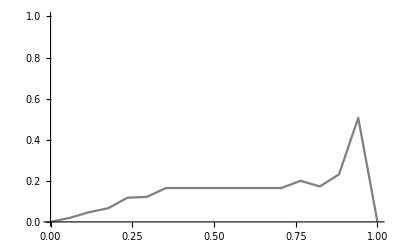

-Graphics3D-

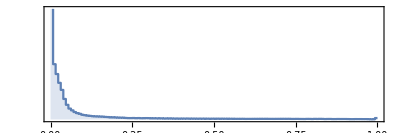

```mathematica
i
tf=Import[tffilelist[[i]],"XML"];
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgba=(#/255.&)/@Transpose[{r,g,b,a}];
colors=RGBColor/@rgba;
defaultcolorfunction=(Blend[{{0., RGBColor[0.05635, 0.081, 0.07687, 0.0166234]}, {0.1, RGBColor[0.8877, 0.2636, 0., 0.114961]}, {0.66, RGBColor[1., 0.9658, 0.4926, 0.665652]}, {1., RGBColor[1., 0.6436, 0.03622, 1.]}}, #1] & );
Transpose[{intensity,colors}]
colorfunction=(Blend[Transpose[{intensity,colors}], #1] & )
rgb=(#/255.&)/@Transpose[{r,g,b}];
colors2=RGBColor/@rgb;
colorfunction2=(Blend[Transpose[{intensity,colors2}], #1] & )
opacity=(#/255.&)/@a;
ListLinePlot[Transpose[{intensity,opacity}],PlotRange->{{0,1},{0,1}},ColorFunction->colorfunction2,PlotLegends->"transfer function"]
Image3D[d[[i]],ColorFunction->colorfunction]
ImageHistogram[d[[i]]]
```

```mathematica
(*start=1+offset;end=500;step=20;
Do[
end2=Min[j+step-1,end];
Module[{list,std,a,b,h,x,y,bins,sumstd,stds,plot1,plot2,result},
result=ParallelTable[
list=d[[i-offset;;i]];
std=ImageAdjust@@ImageApply[StandardDeviation[{##}]&,list];
a=Flatten[ImageData[d[[i]]]];
b=Flatten[ImageData[std]];
h=HistogramList[a];
x=Take[h[[1]],Length[h[[1]]]-1];
y=h[[2]];
plot1=ListLinePlot[Transpose[{x,y}],PlotRange->{{0,1},{0,20000}},ColorFunction->(GrayLevel[#]&),PlotLegends->"intensity histogram"];

bins=ConstantArray[0,Length[y]];
sumstd=ConstantArray[0,Length[y]];
Table[n=IntegerPart[a[[m]]*20]+1;bins[[n]]++;sumstd[[n]]+=b[[m]],{m,1,Length[a]}];
stds=sumstd/bins;
plot2=ListLinePlot[Transpose[{x,stds}],ColorFunction->(GrayLevel[#]&),PlotLegends->"volatility histogram"];
{plot1,plot2}
,{i,j,end2}];
num=Range[j,end2];
MapIndexed[
Export[NotebookDirectory[]<>"smoke2\\"<>IntegerString[num[[First[#2]]],10,3]<>".png",First[#],ImageSize->{640,280}]&;Export[NotebookDirectory[]<>"smoke2_std\\"<>IntegerString[num[[First[#2]]],10,3]<>".png",Last[#],ImageSize->{640,280}]&
,result];
]
,{j,start,end,step}]*)
```

```mathematica
list=Range[0,1,1/255];
Length[list]
```

256

```mathematica
x
y
x2=h[[1]]
```

{0,1/20,1/10,3/20,1/5,1/4,3/10,7/20,2/5,9/20,1/2,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20,1}

{934910,19822,8800,5682,4199,3405,2848,2195,2145,1962,1880,1533,1545,1539,1543,1261,1383,1156,1002,677,513}

{0,1/20,1/10,3/20,1/5,1/4,3/10,7/20,2/5,9/20,1/2,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20,1,21/20}

```mathematica
sum=Total[y]
alpha=Interpolation[Transpose[{intensity,opacity}]]
hist[i_]:=First@FirstPosition[x2,_?(i<#&)]-1
probability[i_]:=N[y[[hist[i]]]/sum]
entropy[i_]:=Module[{p},p=probability[i];-p*Log[p]]
signiﬁcance[i_]:=alpha[i]*entropy[i]
energy[x1_,x2_]:=Sum[signiﬁcance[i],{i,x1,x2,1/255.0}]
```

1000000

InterpolatingFunction[{{0., 1.}}, <>]

```mathematica
hist[0.05]
```

2

```mathematica
Table[{i,hist[i],y[[hist[i]]]},{i,0,1,1/20}]
```

{{0,1,934910},{1/20,2,19822},{1/10,3,8800},{3/20,4,5682},{1/5,5,4199},{1/4,6,3405},{3/10,7,2848},{7/20,8,2195},{2/5,9,2145},{9/20,10,1962},{1/2,11,1880},{11/20,12,1533},{3/5,13,1545},{13/20,14,1539},{7/10,15,1543},{3/4,16,1261},{4/5,17,1383},{17/20,18,1156},{9/10,19,1002},{19/20,20,677},{1,21,513}}

```mathematica
probability[0]
```

0.93491

```mathematica
entropy[0]
```

0.0629241

```mathematica
-0.93491*Log[0.93491]
```

0.0629241

```mathematica
Transpose[{intensity,opacity}]
```

{{0,0.},{0.0588235,0.0196078},{0.117647,0.0470588},{0.176471,0.0666667},{0.235294,0.117647},{0.294118,0.121569},{0.352941,0.164706},{0.411765,0.164706},{0.470588,0.164706},{0.529412,0.164706},{0.588235,0.164706},{0.647059,0.164706},{0.705882,0.164706},{0.764706,0.2},{0.823529,0.172549},{0.882353,0.231373},{0.941176,0.505882},{1,0.}}

```mathematica
alpha=Interpolation[Transpose[{intensity,opacity}]]
```

InterpolatingFunction[{{0., 1.}}, <>]

```mathematica
alpha[0]
```

0.

```mathematica
alpha[0.0588]
```

0.0195974

```mathematica
signiﬁcance[0.058823529411764705]
```

0.00152395

```mathematica
energy[0,0.058823529411764705]
```

0.00943657

```mathematica
list=Table[signiﬁcance[i],{i,0,0.058823529411764705,1/255.}]
```

{0.,0.0000471101,0.000100508,0.000159901,0.000224998,0.000295504,0.000371129,0.000451579,0.000536563,0.000625787,0.000718959,0.000815787,0.000915978,0.00125892,0.0013899,0.00152395}

```mathematica
intensity
```

{0,0.0588235,0.117647,0.176471,0.235294,0.294118,0.352941,0.411765,0.470588,0.529412,0.588235,0.647059,0.705882,0.764706,0.823529,0.882353,0.941176,1}

```mathematica
interval=Table[{intensity[[i]],intensity[[i+1]]},{i,Length[intensity]-1}]
```

{{0,0.0588235},{0.0588235,0.117647},{0.117647,0.176471},{0.176471,0.235294},{0.235294,0.294118},{0.294118,0.352941},{0.352941,0.411765},{0.411765,0.470588},{0.470588,0.529412},{0.529412,0.588235},{0.588235,0.647059},{0.647059,0.705882},{0.705882,0.764706},{0.764706,0.823529},{0.823529,0.882353},{0.882353,0.941176},{0.941176,1}}

```mathematica
edges=energy[#1,#2]&@@@interval
mean=Mean[edges]
Length[edges]
opacity
Length[opacity]
```

{0.00943657,0.0336089,0.0319838,0.0369971,0.0388463,0.0383863,0.0356009,0.0337954,0.0316637,0.0280239,0.0263214,0.0260611,0.0280748,0.0258144,0.0253635,0.0444901,0.0308605}

0.0309017

17

{0.,0.0196078,0.0470588,0.0666667,0.117647,0.121569,0.164706,0.164706,0.164706,0.164706,0.164706,0.164706,0.164706,0.2,0.172549,0.231373,0.505882,0.}

18

```mathematica
MapIndexed[#1&,edges]
```

{0.00943657,0.0336089,0.0319838,0.0369971,0.0388463,0.0383863,0.0356009,0.0337954,0.0316637,0.0280239,0.0263214,0.0260611,0.0280748,0.0258144,0.0253635,0.0444901,0.0308605}

```mathematica
max=0
min = 255
imin=-1
imax=-1
Do[max=If[edges[[i]]>max && opacity[[i]]>0,imax=i;edges[[i]],max];min=If[edges[[i]]<min&& opacity[[i]]>0,imin=i;edges[[i]],min],{i,1,Length[edges]}]
max
imax
min
imin
```

0

255

-1

-1

0.0444901

16

0.0253635

15

```mathematica
First@FirstPosition[edges,_?(#==Max[edges]&)]
```

16

```mathematica
First@FirstPosition[edges,_?(#==Min[edges]&)]
```

1

```mathematica
Position[edges,_?(#>0.02&)]
```

{{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17}}

```mathematica
Table[If[edges[[i]]>mean,edges[[i]]-1/255.0,edges[[i]]+1/255.0],{i,1,Length[edges]}]
```

{0.0133581,0.0296873,0.0280622,0.0330756,0.0349247,0.0344648,0.0316793,0.0298738,0.0277421,0.0319455,0.030243,0.0299826,0.0319964,0.029736,0.0292851,0.0405685,0.0347821}

```mathematica
opacity2=opacity
alpha=Interpolation[Transpose[{intensity,opacity2}]]
Length[opacity2]
```

{0.,0.0196078,0.0470588,0.0666667,0.117647,0.121569,0.164706,0.164706,0.164706,0.164706,0.164706,0.164706,0.164706,0.2,0.172549,0.231373,0.505882,0.}

InterpolatingFunction[{{0., 1.}}, <>]

18

```mathematica
Do[Module[{d,m,list},
d=1/255.0;
alpha=Interpolation[Transpose[{intensity,opacity2}]];
edges=energy[#1,#2]&@@@interval;
m=Mean[edges];
list=Table[If[edges[[i]]>m,-d,d],{i,1,Length[edges]}]
],{100}]
```

```mathematica
edges
```

{0.032966,0.0336089,0.0319838,0.029154,0.0310032,0.0305432,0.0277578,0.0259522,0.0316637,0.0280239,0.0263214,0.0260611,0.0280748,0.0336576,0.0332067,0.0288038,0.0308605}